0

0.07

100

(final_time-initial_time)/numb_intervals

Table::iterb: Iterator {t,inital_time,final_time,step_size} does not have appropriate bounds.

Table[potFunction[t],{t,inital_time,final_time,step_size}]

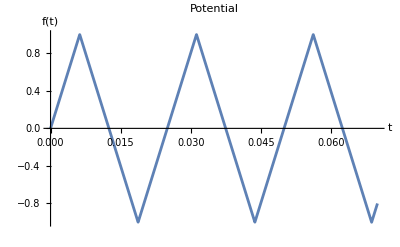

OutputStream[…]

potential.txt

Table::iterb: Iterator {t,inital_time,final_time,step_size} does not have appropriate bounds.

Table[potFunction[t],{t,inital_time,final_time,step_size}]

```mathematica
ClearAll["Global`*"]

inital_time = 0
final_time = 0.07
numb_intervals = 100
step_size = (final_time-initial_time)/numb_intervals

(*Define linear function*)
potFunction[t_]:=TriangleWave[t*40]
vector = Table[ potFunction[t],{t,inital_time,final_time,step_size} ]

(*Plot the linear function over a time range*)
Plot[potFunction[t],{t,0,0.07},PlotRange->All,AxesLabel->{"t","f(t)"},PlotLabel->"Potential"]

f = OpenWrite["potential.txt",FormatType -> OutputForm]

Do[Write[f, potFunction[i]],{i,1,100}]

Close[f]

Print[vector]
```